```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
(*nEFUN[persInds[[#]],,numCONE]*)
nEFUN[name_, pos_, mod_]:=Module[{ind,pers,posP,con,conE,persE,persEB,persEA,persET,out},
(*{3,7,9,11,15,19}*)
Which[name=="DLB", ind=3; posP=pos;,
name=="MUR", ind=7;posP=Drop[pos,1];,
name=="LYE", ind=9;posP=Drop[pos,1];,
name=="PHI", ind=11;posP=Drop[pos,2];,
name=="SED", ind=15;posP=Drop[pos,3];,
name=="AUS", ind=19;posP=Drop[pos,6];];

pers=posP[[All,ind]];
con=posP[[All,1]];
persE=Map[Union[#["BK"],#["EV"]]&,pers];
conE=Map[Union[#["BK"],#["EV"]]&,con];


persEB=Map[Union[persE[[#]],conE[[#]]]&,Range[Length[conE]]];
persEA=Map[Union[persE[[#]],conE[[#+1]]]&,Range[Length[conE]-1]];
persET=Flatten[Prepend[Map[{persEA[[#]],persEB[[#+1]]}&,Range[Length[conE]-1]],{First[persEB]}],1];
(*Print["persET ", persET];*)

out=If[mod=="NUM",Map[Length[#]&,persET],persET];
Return[out];
];

eFUN[name_, pos_,dev_, mod_]:=Module[{persE,persENEG, false,true, out},
persE=nEFUN[name, pos, "STR"];
persENEG=Map[Function[y,Map[Function[x,If[StringQ[x],!x,x[[1]]]],y]],persE];
(*Print["persENEG ", persENEG];*)
false=Map[Intersection[dev,#]&,persENEG];
true=Map[Intersection[dev,#]&,persE];
out=Which[mod=="FALN", Map[Length[#]&,false],
mod=="FAL",false,
mod=="TRUN", Map[Length[#]&,true],
mod=="TRU",true];
Return[out];
];

prozEFunc[name_, eTFL_,eL_]:=Module[{out},
out=Map[Round[ eTFL[[#]]/eL[[#]],0.001]&,Range[Length[eL]]];
Return[out];
];

h[nam_,lTS_]:=Module[{list,k},
k=If[lTS>9,2,1];
list=Which[nam=="DLB",Drop[Range[lTS],0*k],
nam=="MUR",Drop[Range[lTS],1*k],
nam=="LYE",Drop[Range[lTS],1*k],
nam=="PHI",Drop[Range[lTS],2*k],
nam=="SED",Drop[Range[lTS],3*k],
nam=="AUS",Drop[Range[lTS],6*k]
];
Return[list];];

singlePlot2[nam_, dataArrows_,poi_,colS_,conf_, range_, fac1_,fac2_]:=Module[{head,arrows,size, plot1,pointsG,plot2,dataInset,boxInset},

head=Graphics[{Thickness[0.007],Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]}];
arrows=bowedArrowsData[dataArrows];

dataInset={{"E",""},{"Circles", "VV"},{"CONF",ToString[conf]},{"PERS",ToString[nam]}};
boxInset=Text@Grid[dataInset,Background->{None,{Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},
Alignment->{{Left,Center}},ItemSize->{{6,4}},Frame->Darker[Gray,.6],ItemStyle->17,Spacings->{Automatic,.8}];


plot1=Graphics[{Opacity[0.4],colS[[#4]],Arrowheads[{{.012,1,{head,0.01}}}],Thickness[0.007],Arrow[BezierCurve[{#1,#2,#3}]]}&@@@arrows,PlotRange->range,
Frame->True,FrameLabel->{Style["(|SubscriptBox[e, F]|)/(|e|)",20],Style["(|SubscriptBox[e, T]|)/(|e|)",20]}, 
ImageSize->800, ImagePadding->120,Epilog->Inset[Style[boxInset,16],{0.45*range[[2,1]],0.93*range[[2,2]]}]];

(*Print["poi ", poi];*)
size=Map[(Log[poi[[#,3]]]*fac1)+fac2&,Range[Length[poi]]];
(*Print["size ", size];*)
pointsG=Map[Graphics[{Opacity[0.6],Hue[1,0.3],PointSize[size[[#]]],Point[poi[[#]][[1;;2]]]}]&, Range[Length[poi]]];
plot2=Show[Catenate[{{plot1},pointsG}]];

Return[plot2];
];

pointsFunc[name_, threC_, pointsE_]:=Module[{pointsEP,circP,out},
pointsEP=pointsE[name];
circP=threC[name];
(*Print["pointsEP ", pointsEP, " Länge ",Length[pointsEP] ];
Print["circP ", circP, " Länge ",Length[circP] ];*)
out=name->Map[Flatten[{Cases[pointsEP,p_/;p[[3]]==circP[[#,1]]][[1]][[1;;2]],circP[[#,2]]},1]&,
Range[Length[circP]]];
Return[out];]
```

```mathematica
confVal=Get["/home/carla/GDC/CH_Pool/VV_Tables/THRE_RATIO_TIME.txt"];
sigFiles=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_AR_DLB_ALL_Out/*.out"];
tauFiles=FileNames["/home/carla/GDC/TAU2/*.out"];
posFiles=FileNames["/home/carla/GDC/POS/*.txt"];
pos=Map[Get[#]&,posFiles];
names={"DLB","MUR","LYE","PHI","SED","AUS"};
nameI=Map[{#,pos[[8,#]][["name"]]}&,Range[Length[pos[[8]]]]];
persInds=Flatten[Map[Position[nameI,#]&,names],1][[All,1]]
persDrops={0,1,1,2,3,6};
tsSTR=Flatten[Prepend[Map[{"S"<>ToString[#]<>"a","S"<>ToString[#]<>"b"}&,Range[8]],{"S0b"}],1]
timesteps=Range[17];
timeRules=Map[tsSTR[[#]]->timesteps[[#]]&,Range[Length[timesteps]]]

col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]]
```

{3,7,9,11,15,19}

{S0b,S1a,S1b,S2a,S2b,S3a,S3b,S4a,S4b,S5a,S5b,S6a,S6b,S7a,S7b,S8a,S8b}

{S0b→1,S1a→2,S1b→3,S2a→4,S2b→5,S3a→6,S3b→7,S4a→8,S4b→9,S5a→10,S5b→11,S6a→12,S6b→13,S7a→14,S7b→15,S8a→16,S8b→17}

{RGBColor[Rational[1, 17], Rational[1, 17], Rational[16, 17]],RGBColor[Rational[2, 17], Rational[2, 17], Rational[15, 17]],RGBColor[Rational[3, 17], Rational[3, 17], Rational[14, 17]],RGBColor[Rational[4, 17], Rational[4, 17], Rational[13, 17]],RGBColor[Rational[5, 17], Rational[5, 17], Rational[12, 17]],RGBColor[Rational[6, 17], Rational[6, 17], Rational[11, 17]],RGBColor[Rational[7, 17], Rational[7, 17], Rational[10, 17]],RGBColor[Rational[8, 17], Rational[8, 17], Rational[9, 17]],RGBColor[Rational[9, 17], Rational[9, 17], Rational[8, 17]],RGBColor[Rational[10, 17], Rational[10, 17], Rational[7, 17]],RGBColor[Rational[11, 17], Rational[11, 17], Rational[6, 17]],RGBColor[Rational[12, 17], Rational[12, 17], Rational[5, 17]],RGBColor[Rational[13, 17], Rational[13, 17], Rational[4, 17]],RGBColor[Rational[14, 17], Rational[14, 17], Rational[3, 17]],RGBColor[Rational[15, 17], Rational[15, 17], Rational[2, 17]],RGBColor[Rational[16, 17], Rational[16, 17], Rational[1, 17]],RGBColor[1, 1, 0]}

```mathematica
dojCirc=Values[confVal][[All,1]][[All,2]][[All,2]];
zCirc=Values[confVal][[All,2]][[All,2]][[All,2]];
fCirc=Values[confVal][[All,3]][[All,2]][[All,2]];

threDOJ=Association[Map[names[[#]]->dojCirc[[#]]&,Range[Length[names]]]]/.timeRules
threZ=Association[Map[names[[#]]->zCirc[[#]]&,Range[Length[names]]]]/.timeRules;
threF=Association[Map[names[[#]]->fCirc[[#]]&,Range[Length[names]]]]/.timeRules;

(*threDOJ=Association[Map[names[[#]]->Cases[dojCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threZ=Association[Map[names[[#]]->Cases[zCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threF=Association[Map[names[[#]]->Cases[fCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules*)
```

<|DLB→{{17,1}},MUR→{{10,11/18},{11,34/67},{12,34/67},{15,1},{16,1},{17,1}},LYE→{{13,2/3},{14,2/3},{15,1},{17,1}},PHI→{{9,7/10},{10,11/15},{11,7/10},{12,7/10},{13,7/10},{14,7/10},{15,1},{16,1},{17,1}},SED→{{17,1}},AUS→{{13,11/15},{14,11/15},{15,1},{16,1},{17,1}}|>

```mathematica
sigs=Map[N[ToExpression[StringDrop[FindList[#,"sigma "][[1]],6]]]&,sigFiles]
sens=Map[ToExpression[StringDrop[FindList[#,"Number Sentences "][[3]],18]]&,tauFiles]
con=pos[[All,1]];
conE=Map[Union[#["BK"],#["EV"]]&,con];
numCONE=Map[Length[#]&,conE]
(*sensPers=Map[sens[[#]]-numCONE[[#]]&,Range[Length[sens]]]*)
```

{79065.,2.22306×10^7,1.18149×10^8,2.03029×10^8,4.16805×10^9,6.28029×10^10,6.18737×10^11,4.2205×10^12,9.06856×10^12}

{46,65,84,88,102,110,117,123,132}

{8,9,15,17,21,22,22,23,26}

```mathematica
dens=Map[((sens[[#]]-Log[sigs[[#]]])/sens[[#]])&,Range[Length[sens]]]
densPoints=Map[{#-1,dens[[#]]}&,Range[9]]
```

{0.754826,0.739739,0.778721,0.782627,0.782836,0.77397,0.767941,0.763651,0.773971}

{{0,0.754826},{1,0.739739},{2,0.778721},{3,0.782627},{4,0.782836},{5,0.77397},{6,0.767941},{7,0.763651},{8,0.773971}}

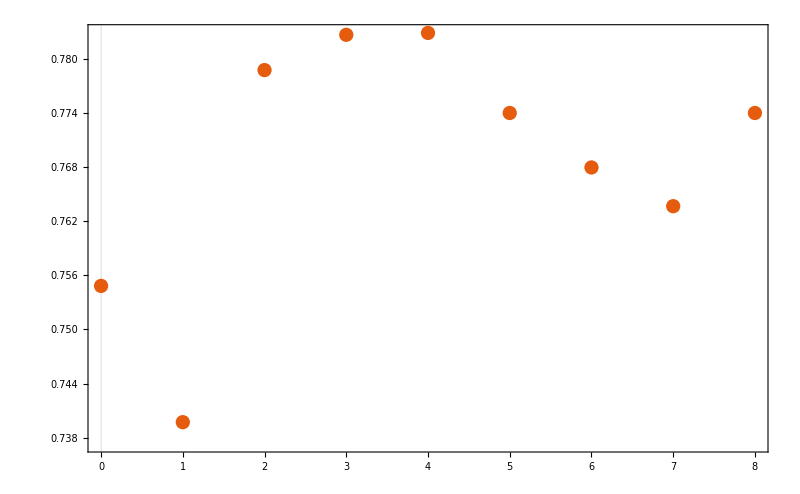

```mathematica
densPlot=ListPlot[densPoints,PlotTheme->"Scientific",ImageSize->800, ImagePadding->120]
```

```mathematica
SetDirectory["/home/carla/GDC/DENS/"]
Put[dens, "GDC_DENS.txt"]
Export["GDC_DENS.jpeg",densPlot]
```

/home/carla/GDC/DENS

GDC_DENS.jpeg

```mathematica
dlb=nEFUN["DLB",pos,"NUM"]
prozEFunc["DLB", dlb,sens]
dlbB=Map[dlb[[#]]&,{1,3,5,7,9,11,13,15,17}]
numCONE
dlbBCORE=dlbB-numCONE
Map[dlbBCORE[[#]]+numCONE[[#+1]]&,Range[Length[numCONE]-1]]
dlbA=Map[dlb[[#]]&,{2,4,6,8,10,12,14,16}]
```

{15,16,22,28,22,24,25,29,33,34,36,36,39,40,42,45,43}

sentPT {46,65,65,84,84,88,88,102,102,110,110,117,117,123,123,132,132}

{0.326,0.246,0.338,0.333,0.262,0.273,0.284,0.284,0.324,0.309,0.327,0.308,0.333,0.325,0.341,0.341,0.326}

{15,22,22,25,33,36,39,42,43}

{8,9,15,17,21,22,22,23,26}

{7,13,7,8,12,14,17,19,17}

{16,28,24,29,34,36,40,45}

{16,28,24,29,34,36,40,45}

```mathematica
eSIZE=Association[Map[names[[#]]->nEFUN[names[[#]],pos,"NUM"]&,Range[Length[names]]]]
(*ePROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eSIZE][[#]],sens]&,Range[Length[names]]]]*)
```

<|DLB→{15,16,22,28,22,24,25,29,33,34,36,36,39,40,42,45,43},MUR→{20,26,25,27,30,34,37,38,41,41,43,44,42,45,45},LYE→{19,25,22,24,26,30,31,32,35,35,36,37,41,44,43},PHI→{20,22,24,28,32,33,35,35,36,37,40,43,41},SED→{25,29,34,35,38,38,39,40,44,47,44},AUS→{40,41,44,47,43}|>

```mathematica
N[{2./20,5./20,8./20}]
{8./19,4./19}
```

{0.1,0.25,0.4}

{0.421053,0.210526}

```mathematica
devABFIN=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/gdc_DEDAB_E_DEV.txt"][[-1]];
```

```mathematica
(*eFALSE=Association[Map[names[[#]]->eFUN[persInds[[#]], Drop[pos,persDrops[[#]]],devABFIN,"FAL"]&,Range[Length[names]]]];*)
(*eFUN[name_, pos_,dev_, mod_]*)
eFALSENUM=Association[Map[names[[#]]->eFUN[names[[#]], pos,devABFIN,"FALN"]&,Range[Length[names]]]]
eTRUENUM=Association[Map[names[[#]]->eFUN[names[[#]], pos,devABFIN,"TRUN"]&,Range[Length[names]]]]
eFALSEPROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eFALSENUM][[#]],Values[eSIZE][[#]]]&,Range[Length[names]]]]
eTRUEPROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eTRUENUM][[#]],Values[eSIZE][[#]]]&,Range[Length[names]]]]
```

<|DLB→{5,5,5,5,1,1,0,0,1,1,2,2,3,3,5,5,0},MUR→{2,2,2,2,2,2,4,4,4,4,7,7,1,1,0},LYE→{2,2,2,2,2,2,3,3,5,5,5,5,3,3,0},PHI→{0,0,0,0,0,0,1,1,2,2,3,3,0},SED→{0,0,3,3,4,4,5,5,6,6,0},AUS→{1,1,2,2,0}|>

<|DLB→{9,10,14,20,18,20,22,26,28,29,30,30,32,33,33,36,39},MUR→{15,21,18,20,22,26,25,26,29,29,28,29,35,38,38},LYE→{14,20,16,18,20,24,24,25,26,26,27,28,34,37,37},PHI→{17,19,21,25,28,29,30,30,30,31,33,36,37},SED→{21,25,26,27,29,29,29,30,33,36,39},AUS→{35,36,38,41,39}|>

<|DLB→{0.333,0.312,0.227,0.179,0.045,0.042,0.,0.,0.03,0.029,0.056,0.056,0.077,0.075,0.119,0.111,0.},MUR→{0.1,0.077,0.08,0.074,0.067,0.059,0.108,0.105,0.098,0.098,0.163,0.159,0.024,0.022,0.},LYE→{0.105,0.08,0.091,0.083,0.077,0.067,0.097,0.094,0.143,0.143,0.139,0.135,0.073,0.068,0.},PHI→{0.,0.,0.,0.,0.,0.,0.029,0.029,0.056,0.054,0.075,0.07,0.},SED→{0.,0.,0.088,0.086,0.105,0.105,0.128,0.125,0.136,0.128,0.},AUS→{0.025,0.024,0.045,0.043,0.}|>

<|DLB→{0.6,0.625,0.636,0.714,0.818,0.833,0.88,0.897,0.848,0.853,0.833,0.833,0.821,0.825,0.786,0.8,0.907},MUR→{0.75,0.808,0.72,0.741,0.733,0.765,0.676,0.684,0.707,0.707,0.651,0.659,0.833,0.844,0.844},LYE→{0.737,0.8,0.727,0.75,0.769,0.8,0.774,0.781,0.743,0.743,0.75,0.757,0.829,0.841,0.86},PHI→{0.85,0.864,0.875,0.893,0.875,0.879,0.857,0.857,0.833,0.838,0.825,0.837,0.902},SED→{0.84,0.862,0.765,0.771,0.763,0.763,0.744,0.75,0.75,0.766,0.886},AUS→{0.875,0.878,0.864,0.872,0.907}|>

```mathematica
pointsE1=Association[Map[Function[y,
y->Map[Function[x,{eFALSEPROZ[y][[x]],eTRUEPROZ[y][[x]],h[y, Length[timesteps]][[x]]}],Range[Length[eFALSEPROZ[y]]]]],names]]
range={{Min[Flatten[Values[pointsE1],1][[All,1]]],Max[Flatten[Values[pointsE1],1][[All,1]]]},
{Min[Flatten[Values[pointsE1],1][[All,2]]],Max[Flatten[Values[pointsE1],1][[All,2]]]}}
```

<|DLB→{{0.333,0.6,1},{0.312,0.625,2},{0.227,0.636,3},{0.179,0.714,4},{0.045,0.818,5},{0.042,0.833,6},{0.,0.88,7},{0.,0.897,8},{0.03,0.848,9},{0.029,0.853,10},{0.056,0.833,11},{0.056,0.833,12},{0.077,0.821,13},{0.075,0.825,14},{0.119,0.786,15},{0.111,0.8,16},{0.,0.907,17}},MUR→{{0.1,0.75,3},{0.077,0.808,4},{0.08,0.72,5},{0.074,0.741,6},{0.067,0.733,7},{0.059,0.765,8},{0.108,0.676,9},{0.105,0.684,10},{0.098,0.707,11},{0.098,0.707,12},{0.163,0.651,13},{0.159,0.659,14},{0.024,0.833,15},{0.022,0.844,16},{0.,0.844,17}},LYE→{{0.105,0.737,3},{0.08,0.8,4},{0.091,0.727,5},{0.083,0.75,6},{0.077,0.769,7},{0.067,0.8,8},{0.097,0.774,9},{0.094,0.781,10},{0.143,0.743,11},{0.143,0.743,12},{0.139,0.75,13},{0.135,0.757,14},{0.073,0.829,15},{0.068,0.841,16},{0.,0.86,17}},PHI→{{0.,0.85,5},{0.,0.864,6},{0.,0.875,7},{0.,0.893,8},{0.,0.875,9},{0.,0.879,10},{0.029,0.857,11},{0.029,0.857,12},{0.056,0.833,13},{0.054,0.838,14},{0.075,0.825,15},{0.07,0.837,16},{0.,0.902,17}},SED→{{0.,0.84,7},{0.,0.862,8},{0.088,0.765,9},{0.086,0.771,10},{0.105,0.763,11},{0.105,0.763,12},{0.128,0.744,13},{0.125,0.75,14},{0.136,0.75,15},{0.128,0.766,16},{0.,0.886,17}},AUS→{{0.025,0.875,13},{0.024,0.878,14},{0.045,0.864,15},{0.043,0.872,16},{0.,0.907,17}}|>

{{0.,0.333},{0.6,0.907}}

```mathematica
threDOJ["MUR"]
Range[Length[threDOJ["MUR"]]]
```

{{10,11/18},{11,34/67},{12,34/67},{15,1},{16,1},{17,1}}

{1,2,3,4,5,6}

```mathematica
pDOJass=Association[Map[pointsFunc[#,threDOJ, pointsE1]&,names]]
pZass=Association[Map[pointsFunc[#,threZ, pointsE1]&,names]];
pFass=Association[Map[pointsFunc[#,threF, pointsE1]&,names]];
```

<|DLB→{{0.,0.907,1}},MUR→{{0.105,0.684,11/18},{0.098,0.707,34/67},{0.098,0.707,34/67},{0.024,0.833,1},{0.022,0.844,1},{0.,0.844,1}},LYE→{{0.139,0.75,2/3},{0.135,0.757,2/3},{0.073,0.829,1},{0.,0.86,1}},PHI→{{0.,0.875,7/10},{0.,0.879,11/15},{0.029,0.857,7/10},{0.029,0.857,7/10},{0.056,0.833,7/10},{0.054,0.838,7/10},{0.075,0.825,1},{0.07,0.837,1},{0.,0.902,1}},SED→{{0.,0.886,1}},AUS→{{0.025,0.875,11/15},{0.024,0.878,11/15},{0.045,0.864,1},{0.043,0.872,1},{0.,0.907,1}}|>

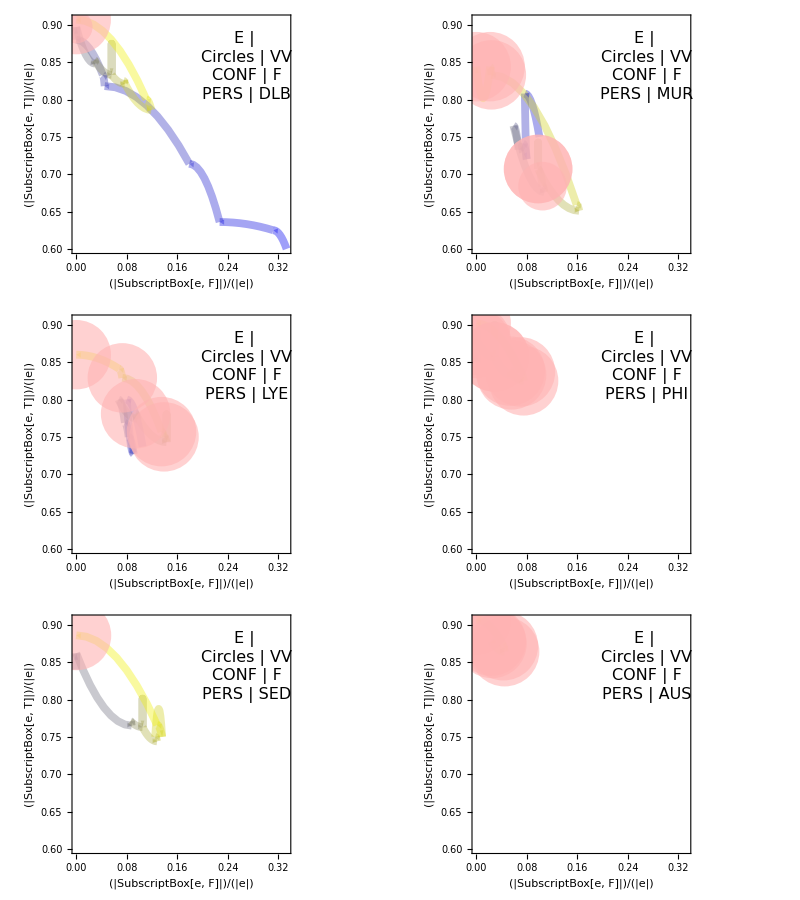

```mathematica
dojTHRE=Map[singlePlot2[#, pointsE1[#],pDOJass[#],col2, "DOJ",range,0.07,0.07]&,names];
dojGrid=Grid[{dojTHRE[[1;;2]],dojTHRE[[3;;4]],dojTHRE[[5;;6]]}];
zTHRE=Map[singlePlot2[#, pointsE1[#],pZass[#],col2, "Z",range,0.07,0.07]&,names];
zGrid=Grid[{zTHRE[[1;;2]],zTHRE[[3;;4]],zTHRE[[5;;6]]}];
fTHRE=Map[singlePlot2[#, pointsE1[#],pFass[#],col2, "F",range,0.07,0.07]&,names];
fGrid=Grid[{fTHRE[[1;;2]],fTHRE[[3;;4]],fTHRE[[5;;6]]}]
```

```mathematica
SetDirectory["/home/carla/GDC/DENS/PROPS2/"]
Export["DOJ_E.jpeg", dojGrid]
Export["Z_E.jpeg", zGrid]
Export["F_E.jpeg", fGrid]
```

/home/carla/GDC/DENS/PROPS2

DOJ_E.jpeg

Z_E.jpeg

F_E.jpeg